```mathematica
Problem 2
```

```mathematica
FindRoot[s==Tanh[4 s/2],{s,0.5}][[1,2]]
```

0.957504

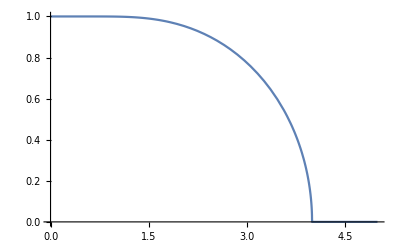

```mathematica
Plot[FindRoot[s==Tanh[4 s/t],{s,0.5}][[1,2]], {t, 0, 5}]
```

```mathematica
Problem 5 Setup
```

Import the data

```mathematica
variances:=Import["/Volumes/1TB Storage Drive/Desktop/senior/Thermal/hw11/variances.csv"]
mags:=
Import["/Volumes/1TB Storage Drive/Desktop/senior/Thermal/hw11/mags.csv"]
varsShort:=
Import["/Volumes/1TB Storage Drive/Desktop/senior/Thermal/hw11/vars_short.csv"]
```

5 a Problem

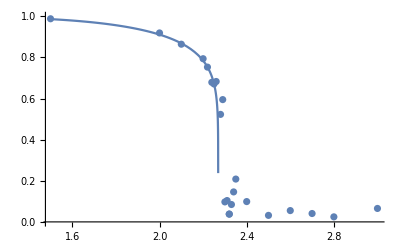

```mathematica
Problem 4a
Show[ListPlot[mags],Plot[(1 - (Sinh[2/T])^-4)^(1/8),{T,1.5,2.27}, PlotRange->All]]
```

```mathematica
Problem 4b
```

```mathematica
(*chi0:=0.00132*)
FindFit[varsShort, chi0 * (T/Tc-1)^-γ, { {γ}, {chi0}, {Tc,2.27}}, T]
```

FindFit::nrlnum: The function value {-0.0437077-0.000315452 ⅈ,-0.077093-0.000219428 ⅈ,-0.0276322-0.0000698487 ⅈ,-0.0276322-0.0000698487 ⅈ,-«20»+0. ⅈ,-«21»+«1»,-0.02184+0. ⅈ,-0.0101965+0. ⅈ,-0.00488619+0. ⅈ,-0.00362087+0. ⅈ} is not a list of real numbers with dimensions {10} at {γ,chi0,Tc} = {-0.58577,-0.00506053,2.32165}.

{γ→-0.58577,chi0→-0.00506053,Tc→2.32165}

I did this problem in two ways. I first tried allowing FindFit to fit for chi0 in addition to gamma and Tc, but this was yielding awful results, even when it is suggested to it that it look near Tc=2.27: {chi0→-0.00506053,γ→-0.58577,Tc→2.32165}

I originally thought that this was just because of bad data, but after spending several hours going back and recollecting all the data, I still get the same bad results.

I was able to cheat this a little bit by manually guessing values of chi0 until Tc approached the appropriate value. This yielded a value for gamma that, while still pretty far off from 7/4, was significantly closer than the -0.58 that was being returned before: {γ→0.880112,Tc→2.26798}

```mathematica
Problem 4c
```

As the system temperature goes to Tc, the correlation length goes to the system size. As the temperature increases from there, the correlation size shrinks.

```mathematica
Problem 4d
```

```mathematica
FindFit[varsShort, chi0^(-4/7) * (T/Tc-1), {{Tc,2.3}}, T]
```

{Tc→2.37919}

Again, this predicted value is quite far away from the expected value of 2.269, likely for the same reasons as above. Strangely, though, this one is actually worse than the previous bad result.


My suspicion here is that my problem lies in Mathematica syntax, as I recollected the data and have poured over the equations several times to ensure that they’re correct. I have no idea what it is.